## Designing LC circuit

## Resonant Frequency of a RLC circuit

```mathematica
Clear[R,L,Cp]
```

```mathematica
Q = 1/R √(L/Cp)  (* In an ideal series RLC circuit. We want a big quality factor  http://en.wikipedia.org/wiki/Q_factor*)
resFreq = 1/√(L Cp)
```

(√(L/Cp))/R

1/(√(Cp L))

```mathematica
http://www.mr-tip.com/serv1.php?type=db1&dbs=Resonance+Frequency
```

```mathematica
The resonance frequency at 1.5 T for  1H,63.86 MHz.  (directy proportional to magnetic strength.
```

```mathematica
63.86*2
```

127.72

```mathematica
Solve[127.72== 1/√(Cp L)] (*do 100 turns of our wire and measure inductance to learn the necessary capacitor*)
```

```mathematica
What energy can we get?
Can I grab the coil from an AM radio?
```

```mathematica
μ0 = 4π 10^-7;
Inductance[r_,N_,Len_] := (μ0 N^2 π r^2)/Len;
SymInductance[r_,N_,Len_] := (μ0 N^2 π r^2)/(2r);
Resonance[C_,L_]:=1/(2π √(C L))
```

```mathematica
Solve[Resonance[5*10^-12,L]== 123.14*10^6]
```

{{L→3.34097×10^-7}}

```mathematica
Solve[Resonance[C,(μ0 N^2 π r^2)/r]== 123.14*10^6/.{C->5*10^-12,r ->0.001*{10,5,2}}]
```

{{N→-1.45454},{N→1.45454}}

```mathematica
Solve[Resonance[C,L]== 123.14*10^6,L]
```

{{L→(1.67048×10^-18)/C}}

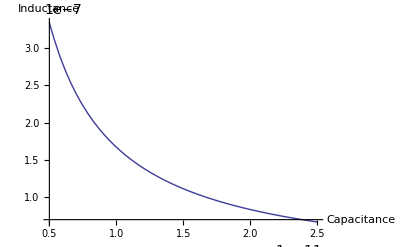

```mathematica
Plot[(1.6704826325111484*^-18)/C,{C,5*10^-12,25*10^-12},AxesLabel->{"Capacitance","Inductance"}]
```

```mathematica
Solve[1.1136550883407655*^-7==(μ0 N^2 π r^2)/Len/.{r]
```

{{Len→0.0567191 N^2}}

```mathematica
1.6704826325111484*^-18/(15*10^-12)
```

1.11366×10^-7

```mathematica
Clear[r]
Solve[L==(μ0 N^2 π r^2)/r,N]
```

{{N→-(500 √10 √L)/(π √r)},{N→(500 √10 √L)/(π √r)}}

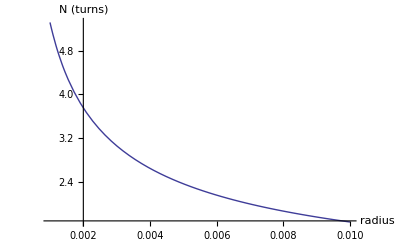

```mathematica
Plot[0.16795598509728568/(√r),{r,0.001,0.01},AxesLabel->{"radius","N (turns)"}]
```

```mathematica
Plot[(1.6704826325111484*^-18)/C,{C,5*10^-12,25*10^-12},AxesLabel->{"Capacitance","Inductance"}]
```

-Graphics-

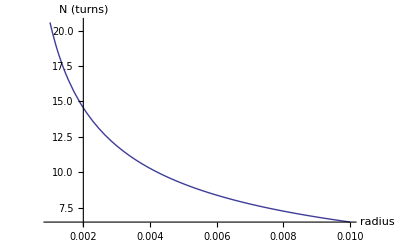

```mathematica
Plot[(500 √10 √((1.6704826325111484*^-18)/C))/(π √r)/.{C->1*10^-12},{r,0.001,0.01},AxesLabel->{"radius","N (turns)"}]
```

```mathematica
Solve[(1.6704826325111484*^-18)/C==(μ0 N^2 π r^2)/Len,N]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N→-(6.50491×10^-7 √Len)/(√C r)},{N→(6.50491×10^-7 √Len)/(√C r)}}

```mathematica
{Nturn =(6.504907331776487*^-7 √Len)/(√Cp r);
StringForm["For C=``, Number of turns N =``",N[Cp],Nturn]}/.{Cp->1*10^-12,Len->0.018,r->0.0035}
```

{For C=1/1000000000000, Number of turns N =24.935}

```mathematica
(c1 c2)/(c1+c2)==ctot
```

1/(1/c1+1/c2)==ctot

```mathematica
(r^2 N^2)/(9 r+10 ell)
```

(N^2 r^2)/(10 ell+9 r)

```mathematica
Clear[a,b]
254/(10000(10a+9b))
```

```mathematica
N[(5000/127 10 a+5000/127 9 b)]
```

```mathematica
Rationalize[393.7007874015748 a+354.3307086614173 b]
```

(50000 a)/127+(45000 b)/127

```mathematica
39.37007874015748 (10. a+9. b)
```

```mathematica
Rationalize[0.0254/(9 r+10 ell)]
```

127/(5000 (10 ell+9 r))

```mathematica
0.0254*10^6
```

25400.

### Harvest Energy from graident -- can we learn something about inductive coupling to do better than Newtons law of Induction

```mathematica
SlewRate = 15;(* 150T/m/sec at 10cm from center = 15 T/sec*)
Nt = 10000; (*num turns*)
r = 0.1;(*radius of coil in m*)
Voltage = Nt SlewRate π r^2
```

4712.39

```mathematica
Clear[r]
N[Solve[Nt SlewRate π r^2==100,r]]
```

{{r→-0.0145673},{r→0.0145673}}

```mathematica
Voltage = N*SlewRate π r^2
```